# Call Python to compute CY metrics

The easiest thing to get started would be to just run the entire notebook

In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and Mathematica versions, setup will automatically apply a bug fix. The program will create a text file (with the same name as the notebook, plus extension “-cymetricsettings.txt”, at the same location as the notebook file) that indicates which virtual environment to use for future runs.

If you want to see the Documentation for any of the functions, run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values.

More advanced (if you do not want to just call Setup[] and be done with it):
1.) If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package for the web.
You can also download the package file and copy it to Mathematica’s Application folder. Too find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/pythoncymetric/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and run with <<cymetric`

```mathematica
Get["https://raw.githubusercontent.com/pythoncymetric/cymetric/main/cymetric/wolfram/cymetric.m"];
```

```mathematica
(*Path where the virtual environment for python will be created. Defaults to the User's Desktop*)
PathToVenv=FileNameJoin[{$HomeDirectory,"Desktop/mathematica-venv"}];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
python=Setup[PathToVenv];
```

## Quintic

### Compute Points and Metric

To look at the parameters and options of a function, simply call ?<FunctionName> and Options[<FunctionName>]

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000,Precision→20,VolJNorm→1,Python→Null,Session→Null,Dir→/Users/ruehle/GitHub/cymetric/notebooks/test,Verbose→3}

Now we generate some points

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"Quintic"}];
NNModel="PhiFS";
session=GetSession[];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+10 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
{res,session}=GeneratePoints[poly,{4},"Points"->100000,"KahlerModuli"->{1},"Session"->session,"Dir"->outDir,"VolJNorm"->5];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Variables have been assigned to the ambient space factors as follows:

1.) P^4: {z_0,z_1,z_2,z_3,z_4}

Generating 100000 points...

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Number of points on CY from one ambient space intersection: 5

Now generating 100000 points...

done.

Writing points to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/points.pickle

DEBUG:mathematica:Using output directory /Users/ruehle/GitHub/cymetric/notebooks/Quintic

DEBUG:mathematica:Ambient space: P^4

DEBUG:mathematica:Kahler moduli: [1]

DEBUG:mathematica:{'outdir': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic', 'logger_level': 10, 'num_pts': 100000, 'monomials': array([[[5, 0, 0, 0, 0], [1, 1, 1, 1, 1], [0, 5, 0, 0, 0], [0, 0, 5, 0, 0], [0, 0, 0, 5, 0], [0, 0, 0, 0, 5]]]), 'coeffs': array([[ 1, 10, 1, 1, 1, 1]]), 'k_moduli': array([1]), 'ambient_dims': array([4]), 'precision': 20, 'vol_j_norm': 5, 'selected_t': array([1]), 'point_file_path': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic/points.pickle'}

INFO:mathematica:Saving point generator to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/point_gen.pickle

INFO:mathematica:Computing derivatives of J_FS, Omega, ...

DEBUG:mathematica:done

Now we train the NN. We choose the PhiFS model here. (Training can be made faster if one sets “EvaluateModel”->False)

```mathematica
{history,session}=TrainNN["Model"->NNModel,"HiddenLayers"->{64,64,64},"ActivationFunctions"->{"gelu","gelu","gelu"},"Epochs"->50,"BatchSize"->64,"Session"->session,"EvaluateModel"->True,"Dir"->outDir,"Verbose"->3];
```

{
        'outdir':        "/Users/ruehle/GitHub/cymetric/notebooks/Quintic",
        'logger_level':  logging.DEBUG,
        'model':         "PhiFS",
        'callbacks':     True,
        'n_hiddens':     [64, 64, 64],
		'acts':          ["gelu", "gelu", "gelu"],
		'n_epochs':      50,
		'batch_size':    64,
		'alphas':        [1., 1., 1., 1., 1.],
        'toric_data_path':""
       }

DEBUG:mathematica:{'outdir': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic', 'logger_level': 10, 'model': 'PhiFS', 'callbacks': True, 'n_hiddens': array([64, 64, 64]), 'acts': array(['gelu', 'gelu', 'gelu'], dtype='<U4'), 'n_epochs': 50, 'batch_size': 64, 'alphas': array([1., 1., 1., 1., 1.]), 'toric_data_path': ''}

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Model: "sequential"

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica: Layer (type)                Output Shape              Param #

DEBUG:mathematica:=================================================================

DEBUG:mathematica: dense (Dense)               (None, 64)                704

DEBUG:mathematica:

DEBUG:mathematica: dense_1 (Dense)             (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_2 (Dense)             (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_3 (Dense)             (None, 1)                 64

DEBUG:mathematica:

DEBUG:mathematica:=================================================================

DEBUG:mathematica:Total params: 9,088

DEBUG:mathematica:Trainable params: 9,088

DEBUG:mathematica:Non-trainable params: 0

DEBUG:mathematica:_________________________________________________________________

- Sigma measure val:      0.2522

- Kaehler measure val:    5.4874e-15

- Transition measure val: 0.0195

- Ricci measure val:      0.8345

- Volk val:               4.3547

Epoch 1/50

- Sigma measure val:      0.1391

- Kaehler measure val:    5.4333e-15

- Transition measure val: 0.0031

- Ricci measure val:      1.3749

- Volk val:               4.8211

1407/1407 - 19s - sigma_loss: 0.1619 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0055 - volk_loss: 0.0000e+00 - sigma_val: 0.1391 - kaehler_val: 5.4333e-15 - transition_val: 0.0031 - ricci_val: 1.3749 - volk_val: 4.8211 - 19s/epoch - 14ms/step

Epoch 2/50

- Sigma measure val:      0.1229

- Kaehler measure val:    5.6989e-15

- Transition measure val: 0.0016

- Ricci measure val:      0.9496

- Volk val:               4.9529

1407/1407 - 17s - sigma_loss: 0.1357 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0022 - volk_loss: 0.0000e+00 - sigma_val: 0.1229 - kaehler_val: 5.6989e-15 - transition_val: 0.0016 - ricci_val: 0.9496 - volk_val: 4.9529 - 17s/epoch - 12ms/step

Epoch 3/50

- Sigma measure val:      0.1014

- Kaehler measure val:    5.9512e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.6825

- Volk val:               4.7613

1407/1407 - 17s - sigma_loss: 0.1161 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0021 - volk_loss: 0.0000e+00 - sigma_val: 0.1014 - kaehler_val: 5.9512e-15 - transition_val: 0.0026 - ricci_val: 0.6825 - volk_val: 4.7613 - 17s/epoch - 12ms/step

Epoch 4/50

- Sigma measure val:      0.0929

- Kaehler measure val:    6.2711e-15

- Transition measure val: 0.0021

- Ricci measure val:      0.6784

- Volk val:               4.9757

1407/1407 - 18s - sigma_loss: 0.0914 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0024 - volk_loss: 0.0000e+00 - sigma_val: 0.0929 - kaehler_val: 6.2711e-15 - transition_val: 0.0021 - ricci_val: 0.6784 - volk_val: 4.9757 - 18s/epoch - 12ms/step

Epoch 5/50

- Sigma measure val:      0.0820

- Kaehler measure val:    6.2050e-15

- Transition measure val: 0.0018

- Ricci measure val:      0.6265

- Volk val:               5.0074

1407/1407 - 16s - sigma_loss: 0.0804 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0020 - volk_loss: 0.0000e+00 - sigma_val: 0.0820 - kaehler_val: 6.2050e-15 - transition_val: 0.0018 - ricci_val: 0.6265 - volk_val: 5.0074 - 16s/epoch - 12ms/step

Epoch 6/50

- Sigma measure val:      0.0798

- Kaehler measure val:    6.0735e-15

- Transition measure val: 0.0015

- Ricci measure val:      0.6070

- Volk val:               4.7736

1407/1407 - 16s - sigma_loss: 0.0743 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0016 - volk_loss: 0.0000e+00 - sigma_val: 0.0798 - kaehler_val: 6.0735e-15 - transition_val: 0.0015 - ricci_val: 0.6070 - volk_val: 4.7736 - 16s/epoch - 11ms/step

Epoch 7/50

- Sigma measure val:      0.0762

- Kaehler measure val:    6.1826e-15

- Transition measure val: 0.0010

- Ricci measure val:      0.5417

- Volk val:               4.8813

1407/1407 - 16s - sigma_loss: 0.0705 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0012 - volk_loss: 0.0000e+00 - sigma_val: 0.0762 - kaehler_val: 6.1826e-15 - transition_val: 0.0010 - ricci_val: 0.5417 - volk_val: 4.8813 - 16s/epoch - 11ms/step

Epoch 8/50

- Sigma measure val:      0.0772

- Kaehler measure val:    6.1301e-15

- Transition measure val: 8.2612e-04

- Ricci measure val:      0.5088

- Volk val:               4.8376

1407/1407 - 17s - sigma_loss: 0.0685 - kaehler_loss: 0.0000e+00 - transition_loss: 9.1457e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0772 - kaehler_val: 6.1301e-15 - transition_val: 8.2612e-04 - ricci_val: 0.5088 - volk_val: 4.8376 - 17s/epoch - 12ms/step

Epoch 9/50

- Sigma measure val:      0.0764

- Kaehler measure val:    5.8569e-15

- Transition measure val: 6.7623e-04

- Ricci measure val:      0.4897

- Volk val:               4.8756

1407/1407 - 16s - sigma_loss: 0.0671 - kaehler_loss: 0.0000e+00 - transition_loss: 7.6486e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0764 - kaehler_val: 5.8569e-15 - transition_val: 6.7623e-04 - ricci_val: 0.4897 - volk_val: 4.8756 - 16s/epoch - 12ms/step

Epoch 10/50

- Sigma measure val:      0.0765

- Kaehler measure val:    6.0051e-15

- Transition measure val: 6.4425e-04

- Ricci measure val:      0.4988

- Volk val:               4.9282

1407/1407 - 18s - sigma_loss: 0.0659 - kaehler_loss: 0.0000e+00 - transition_loss: 6.7408e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0765 - kaehler_val: 6.0051e-15 - transition_val: 6.4425e-04 - ricci_val: 0.4988 - volk_val: 4.9282 - 18s/epoch - 13ms/step

Epoch 11/50

- Sigma measure val:      0.0756

- Kaehler measure val:    5.8998e-15

- Transition measure val: 6.0101e-04

- Ricci measure val:      0.4883

- Volk val:               4.8289

1407/1407 - 20s - sigma_loss: 0.0653 - kaehler_loss: 0.0000e+00 - transition_loss: 6.2043e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0756 - kaehler_val: 5.8998e-15 - transition_val: 6.0101e-04 - ricci_val: 0.4883 - volk_val: 4.8289 - 20s/epoch - 14ms/step

Epoch 12/50

- Sigma measure val:      0.0722

- Kaehler measure val:    5.8803e-15

- Transition measure val: 5.5040e-04

- Ricci measure val:      0.4993

- Volk val:               4.9148

1407/1407 - 17s - sigma_loss: 0.0644 - kaehler_loss: 0.0000e+00 - transition_loss: 5.7732e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0722 - kaehler_val: 5.8803e-15 - transition_val: 5.5040e-04 - ricci_val: 0.4993 - volk_val: 4.9148 - 17s/epoch - 12ms/step

Epoch 13/50

- Sigma measure val:      0.0712

- Kaehler measure val:    5.9292e-15

- Transition measure val: 5.5456e-04

- Ricci measure val:      0.5009

- Volk val:               4.9819

1407/1407 - 17s - sigma_loss: 0.0635 - kaehler_loss: 0.0000e+00 - transition_loss: 5.6198e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0712 - kaehler_val: 5.9292e-15 - transition_val: 5.5456e-04 - ricci_val: 0.5009 - volk_val: 4.9819 - 17s/epoch - 12ms/step

Epoch 14/50

- Sigma measure val:      0.0709

- Kaehler measure val:    5.8657e-15

- Transition measure val: 5.1961e-04

- Ricci measure val:      0.4762

- Volk val:               4.8409

1407/1407 - 16s - sigma_loss: 0.0623 - kaehler_loss: 0.0000e+00 - transition_loss: 5.4169e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0709 - kaehler_val: 5.8657e-15 - transition_val: 5.1961e-04 - ricci_val: 0.4762 - volk_val: 4.8409 - 16s/epoch - 11ms/step

Epoch 15/50

- Sigma measure val:      0.0689

- Kaehler measure val:    5.9529e-15

- Transition measure val: 5.2084e-04

- Ricci measure val:      0.4798

- Volk val:               4.9254

1407/1407 - 18s - sigma_loss: 0.0614 - kaehler_loss: 0.0000e+00 - transition_loss: 5.3905e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0689 - kaehler_val: 5.9529e-15 - transition_val: 5.2084e-04 - ricci_val: 0.4798 - volk_val: 4.9254 - 18s/epoch - 12ms/step

Epoch 16/50

- Sigma measure val:      0.0678

- Kaehler measure val:    5.8939e-15

- Transition measure val: 5.2257e-04

- Ricci measure val:      0.4771

- Volk val:               4.9236

1407/1407 - 18s - sigma_loss: 0.0602 - kaehler_loss: 0.0000e+00 - transition_loss: 5.4291e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0678 - kaehler_val: 5.8939e-15 - transition_val: 5.2257e-04 - ricci_val: 0.4771 - volk_val: 4.9236 - 18s/epoch - 13ms/step

Epoch 17/50

- Sigma measure val:      0.0656

- Kaehler measure val:    5.9813e-15

- Transition measure val: 5.5657e-04

- Ricci measure val:      0.4896

- Volk val:               4.9549

1407/1407 - 17s - sigma_loss: 0.0588 - kaehler_loss: 0.0000e+00 - transition_loss: 5.4610e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0656 - kaehler_val: 5.9813e-15 - transition_val: 5.5657e-04 - ricci_val: 0.4896 - volk_val: 4.9549 - 17s/epoch - 12ms/step

Epoch 18/50

- Sigma measure val:      0.0631

- Kaehler measure val:    5.8907e-15

- Transition measure val: 5.4300e-04

- Ricci measure val:      0.4694

- Volk val:               4.8929

1407/1407 - 18s - sigma_loss: 0.0570 - kaehler_loss: 0.0000e+00 - transition_loss: 5.5256e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0631 - kaehler_val: 5.8907e-15 - transition_val: 5.4300e-04 - ricci_val: 0.4694 - volk_val: 4.8929 - 18s/epoch - 13ms/step

Epoch 19/50

- Sigma measure val:      0.0604

- Kaehler measure val:    5.9906e-15

- Transition measure val: 5.5911e-04

- Ricci measure val:      0.4824

- Volk val:               4.9636

1407/1407 - 17s - sigma_loss: 0.0552 - kaehler_loss: 0.0000e+00 - transition_loss: 5.5477e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0604 - kaehler_val: 5.9906e-15 - transition_val: 5.5911e-04 - ricci_val: 0.4824 - volk_val: 4.9636 - 17s/epoch - 12ms/step

Epoch 20/50

- Sigma measure val:      0.0593

- Kaehler measure val:    6.0832e-15

- Transition measure val: 5.2135e-04

- Ricci measure val:      0.4644

- Volk val:               4.9713

1407/1407 - 19s - sigma_loss: 0.0529 - kaehler_loss: 0.0000e+00 - transition_loss: 5.5484e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0593 - kaehler_val: 6.0832e-15 - transition_val: 5.2135e-04 - ricci_val: 0.4644 - volk_val: 4.9713 - 19s/epoch - 13ms/step

Epoch 21/50

- Sigma measure val:      0.0551

- Kaehler measure val:    6.1346e-15

- Transition measure val: 5.1996e-04

- Ricci measure val:      0.4604

- Volk val:               4.9879

1407/1407 - 17s - sigma_loss: 0.0507 - kaehler_loss: 0.0000e+00 - transition_loss: 5.5568e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0551 - kaehler_val: 6.1346e-15 - transition_val: 5.1996e-04 - ricci_val: 0.4604 - volk_val: 4.9879 - 17s/epoch - 12ms/step

Epoch 22/50

- Sigma measure val:      0.0533

- Kaehler measure val:    6.1819e-15

- Transition measure val: 5.3089e-04

- Ricci measure val:      0.4416

- Volk val:               4.9521

1407/1407 - 17s - sigma_loss: 0.0486 - kaehler_loss: 0.0000e+00 - transition_loss: 5.4328e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0533 - kaehler_val: 6.1819e-15 - transition_val: 5.3089e-04 - ricci_val: 0.4416 - volk_val: 4.9521 - 17s/epoch - 12ms/step

Epoch 23/50

- Sigma measure val:      0.0509

- Kaehler measure val:    6.2586e-15

- Transition measure val: 5.1681e-04

- Ricci measure val:      0.4383

- Volk val:               4.9943

1407/1407 - 16s - sigma_loss: 0.0469 - kaehler_loss: 0.0000e+00 - transition_loss: 5.4247e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0509 - kaehler_val: 6.2586e-15 - transition_val: 5.1681e-04 - ricci_val: 0.4383 - volk_val: 4.9943 - 16s/epoch - 11ms/step

Epoch 24/50

- Sigma measure val:      0.0508

- Kaehler measure val:    6.3976e-15

- Transition measure val: 5.1797e-04

- Ricci measure val:      0.4398

- Volk val:               5.0127

1407/1407 - 17s - sigma_loss: 0.0455 - kaehler_loss: 0.0000e+00 - transition_loss: 5.4108e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0508 - kaehler_val: 6.3976e-15 - transition_val: 5.1797e-04 - ricci_val: 0.4398 - volk_val: 5.0127 - 17s/epoch - 12ms/step

Epoch 25/50

- Sigma measure val:      0.0483

- Kaehler measure val:    6.1418e-15

- Transition measure val: 4.8814e-04

- Ricci measure val:      0.4161

- Volk val:               4.9538

1407/1407 - 17s - sigma_loss: 0.0440 - kaehler_loss: 0.0000e+00 - transition_loss: 5.2731e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0483 - kaehler_val: 6.1418e-15 - transition_val: 4.8814e-04 - ricci_val: 0.4161 - volk_val: 4.9538 - 17s/epoch - 12ms/step

Epoch 26/50

- Sigma measure val:      0.0460

- Kaehler measure val:    6.3959e-15

- Transition measure val: 5.0138e-04

- Ricci measure val:      0.4274

- Volk val:               5.0019

1407/1407 - 17s - sigma_loss: 0.0428 - kaehler_loss: 0.0000e+00 - transition_loss: 5.0690e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0460 - kaehler_val: 6.3959e-15 - transition_val: 5.0138e-04 - ricci_val: 0.4274 - volk_val: 5.0019 - 17s/epoch - 12ms/step

Epoch 27/50

- Sigma measure val:      0.0461

- Kaehler measure val:    6.2835e-15

- Transition measure val: 4.9048e-04

- Ricci measure val:      0.4194

- Volk val:               4.9606

1407/1407 - 17s - sigma_loss: 0.0417 - kaehler_loss: 0.0000e+00 - transition_loss: 5.0741e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0461 - kaehler_val: 6.2835e-15 - transition_val: 4.9048e-04 - ricci_val: 0.4194 - volk_val: 4.9606 - 17s/epoch - 12ms/step

Epoch 28/50

- Sigma measure val:      0.0440

- Kaehler measure val:    6.3467e-15

- Transition measure val: 4.8975e-04

- Ricci measure val:      0.4243

- Volk val:               4.9531

1407/1407 - 16s - sigma_loss: 0.0407 - kaehler_loss: 0.0000e+00 - transition_loss: 4.8383e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0440 - kaehler_val: 6.3467e-15 - transition_val: 4.8975e-04 - ricci_val: 0.4243 - volk_val: 4.9531 - 16s/epoch - 11ms/step

Epoch 29/50

- Sigma measure val:      0.0446

- Kaehler measure val:    6.1596e-15

- Transition measure val: 4.2098e-04

- Ricci measure val:      0.4031

- Volk val:               4.9798

1407/1407 - 17s - sigma_loss: 0.0398 - kaehler_loss: 0.0000e+00 - transition_loss: 4.6647e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0446 - kaehler_val: 6.1596e-15 - transition_val: 4.2098e-04 - ricci_val: 0.4031 - volk_val: 4.9798 - 17s/epoch - 12ms/step

Epoch 30/50

- Sigma measure val:      0.0413

- Kaehler measure val:    6.2754e-15

- Transition measure val: 4.1264e-04

- Ricci measure val:      0.4058

- Volk val:               4.9835

1407/1407 - 16s - sigma_loss: 0.0391 - kaehler_loss: 0.0000e+00 - transition_loss: 4.4349e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0413 - kaehler_val: 6.2754e-15 - transition_val: 4.1264e-04 - ricci_val: 0.4058 - volk_val: 4.9835 - 16s/epoch - 11ms/step

Epoch 31/50

- Sigma measure val:      0.0415

- Kaehler measure val:    6.2991e-15

- Transition measure val: 3.8622e-04

- Ricci measure val:      0.3955

- Volk val:               4.9817

1407/1407 - 16s - sigma_loss: 0.0381 - kaehler_loss: 0.0000e+00 - transition_loss: 4.2310e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0415 - kaehler_val: 6.2991e-15 - transition_val: 3.8622e-04 - ricci_val: 0.3955 - volk_val: 4.9817 - 16s/epoch - 11ms/step

Epoch 32/50

- Sigma measure val:      0.0415

- Kaehler measure val:    6.3397e-15

- Transition measure val: 3.8394e-04

- Ricci measure val:      0.3960

- Volk val:               4.9912

1407/1407 - 16s - sigma_loss: 0.0370 - kaehler_loss: 0.0000e+00 - transition_loss: 4.0265e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0415 - kaehler_val: 6.3397e-15 - transition_val: 3.8394e-04 - ricci_val: 0.3960 - volk_val: 4.9912 - 16s/epoch - 12ms/step

Epoch 33/50

- Sigma measure val:      0.0398

- Kaehler measure val:    6.2989e-15

- Transition measure val: 3.7101e-04

- Ricci measure val:      0.3941

- Volk val:               5.0212

1407/1407 - 17s - sigma_loss: 0.0364 - kaehler_loss: 0.0000e+00 - transition_loss: 3.8526e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0398 - kaehler_val: 6.2989e-15 - transition_val: 3.7101e-04 - ricci_val: 0.3941 - volk_val: 5.0212 - 17s/epoch - 12ms/step

Epoch 34/50

- Sigma measure val:      0.0392

- Kaehler measure val:    6.1455e-15

- Transition measure val: 3.7970e-04

- Ricci measure val:      0.3920

- Volk val:               4.9732

1407/1407 - 18s - sigma_loss: 0.0354 - kaehler_loss: 0.0000e+00 - transition_loss: 3.6452e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0392 - kaehler_val: 6.1455e-15 - transition_val: 3.7970e-04 - ricci_val: 0.3920 - volk_val: 4.9732 - 18s/epoch - 13ms/step

Epoch 35/50

- Sigma measure val:      0.0390

- Kaehler measure val:    6.1660e-15

- Transition measure val: 3.0985e-04

- Ricci measure val:      0.3881

- Volk val:               4.9812

1407/1407 - 16s - sigma_loss: 0.0344 - kaehler_loss: 0.0000e+00 - transition_loss: 3.4419e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0390 - kaehler_val: 6.1660e-15 - transition_val: 3.0985e-04 - ricci_val: 0.3881 - volk_val: 4.9812 - 16s/epoch - 12ms/step

Epoch 36/50

- Sigma measure val:      0.0359

- Kaehler measure val:    6.1668e-15

- Transition measure val: 3.2118e-04

- Ricci measure val:      0.3959

- Volk val:               5.0230

1407/1407 - 16s - sigma_loss: 0.0334 - kaehler_loss: 0.0000e+00 - transition_loss: 3.2120e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0359 - kaehler_val: 6.1668e-15 - transition_val: 3.2118e-04 - ricci_val: 0.3959 - volk_val: 5.0230 - 16s/epoch - 12ms/step

Epoch 37/50

- Sigma measure val:      0.0352

- Kaehler measure val:    6.1145e-15

- Transition measure val: 2.7694e-04

- Ricci measure val:      0.3784

- Volk val:               4.9482

1407/1407 - 16s - sigma_loss: 0.0324 - kaehler_loss: 0.0000e+00 - transition_loss: 3.0618e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0352 - kaehler_val: 6.1145e-15 - transition_val: 2.7694e-04 - ricci_val: 0.3784 - volk_val: 4.9482 - 16s/epoch - 11ms/step

Epoch 38/50

- Sigma measure val:      0.0348

- Kaehler measure val:    6.1514e-15

- Transition measure val: 2.6601e-04

- Ricci measure val:      0.3877

- Volk val:               4.9879

1407/1407 - 17s - sigma_loss: 0.0317 - kaehler_loss: 0.0000e+00 - transition_loss: 2.9132e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0348 - kaehler_val: 6.1514e-15 - transition_val: 2.6601e-04 - ricci_val: 0.3877 - volk_val: 4.9879 - 17s/epoch - 12ms/step

Epoch 39/50

- Sigma measure val:      0.0339

- Kaehler measure val:    6.1570e-15

- Transition measure val: 2.9587e-04

- Ricci measure val:      0.3941

- Volk val:               5.0220

1407/1407 - 17s - sigma_loss: 0.0308 - kaehler_loss: 0.0000e+00 - transition_loss: 2.7702e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0339 - kaehler_val: 6.1570e-15 - transition_val: 2.9587e-04 - ricci_val: 0.3941 - volk_val: 5.0220 - 17s/epoch - 12ms/step

Epoch 40/50

- Sigma measure val:      0.0326

- Kaehler measure val:    6.0917e-15

- Transition measure val: 2.8876e-04

- Ricci measure val:      0.3868

- Volk val:               5.0009

1407/1407 - 18s - sigma_loss: 0.0301 - kaehler_loss: 0.0000e+00 - transition_loss: 2.7869e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0326 - kaehler_val: 6.0917e-15 - transition_val: 2.8876e-04 - ricci_val: 0.3868 - volk_val: 5.0009 - 18s/epoch - 13ms/step

Epoch 41/50

- Sigma measure val:      0.0333

- Kaehler measure val:    5.9467e-15

- Transition measure val: 2.6131e-04

- Ricci measure val:      0.3891

- Volk val:               4.9706

1407/1407 - 17s - sigma_loss: 0.0295 - kaehler_loss: 0.0000e+00 - transition_loss: 2.7269e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0333 - kaehler_val: 5.9467e-15 - transition_val: 2.6131e-04 - ricci_val: 0.3891 - volk_val: 4.9706 - 17s/epoch - 12ms/step

Epoch 42/50

- Sigma measure val:      0.0323

- Kaehler measure val:    6.1307e-15

- Transition measure val: 2.7395e-04

- Ricci measure val:      0.3917

- Volk val:               5.0537

1407/1407 - 17s - sigma_loss: 0.0289 - kaehler_loss: 0.0000e+00 - transition_loss: 2.7159e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0323 - kaehler_val: 6.1307e-15 - transition_val: 2.7395e-04 - ricci_val: 0.3917 - volk_val: 5.0537 - 17s/epoch - 12ms/step

Epoch 43/50

- Sigma measure val:      0.0299

- Kaehler measure val:    6.0515e-15

- Transition measure val: 2.6229e-04

- Ricci measure val:      0.3748

- Volk val:               4.9820

1407/1407 - 17s - sigma_loss: 0.0285 - kaehler_loss: 0.0000e+00 - transition_loss: 2.7067e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0299 - kaehler_val: 6.0515e-15 - transition_val: 2.6229e-04 - ricci_val: 0.3748 - volk_val: 4.9820 - 17s/epoch - 12ms/step

Epoch 44/50

- Sigma measure val:      0.0317

- Kaehler measure val:    5.9647e-15

- Transition measure val: 2.7603e-04

- Ricci measure val:      0.3676

- Volk val:               4.9646

1407/1407 - 17s - sigma_loss: 0.0279 - kaehler_loss: 0.0000e+00 - transition_loss: 2.6953e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0317 - kaehler_val: 5.9647e-15 - transition_val: 2.7603e-04 - ricci_val: 0.3676 - volk_val: 4.9646 - 17s/epoch - 12ms/step

Epoch 45/50

- Sigma measure val:      0.0293

- Kaehler measure val:    6.0502e-15

- Transition measure val: 2.6838e-04

- Ricci measure val:      0.3679

- Volk val:               5.0063

1407/1407 - 18s - sigma_loss: 0.0276 - kaehler_loss: 0.0000e+00 - transition_loss: 2.7077e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0293 - kaehler_val: 6.0502e-15 - transition_val: 2.6838e-04 - ricci_val: 0.3679 - volk_val: 5.0063 - 18s/epoch - 12ms/step

Epoch 46/50

- Sigma measure val:      0.0294

- Kaehler measure val:    5.9624e-15

- Transition measure val: 2.8225e-04

- Ricci measure val:      0.3749

- Volk val:               4.9635

1407/1407 - 18s - sigma_loss: 0.0272 - kaehler_loss: 0.0000e+00 - transition_loss: 2.6756e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0294 - kaehler_val: 5.9624e-15 - transition_val: 2.8225e-04 - ricci_val: 0.3749 - volk_val: 4.9635 - 18s/epoch - 13ms/step

Epoch 47/50

- Sigma measure val:      0.0291

- Kaehler measure val:    6.0914e-15

- Transition measure val: 2.7244e-04

- Ricci measure val:      0.3880

- Volk val:               5.0284

1407/1407 - 17s - sigma_loss: 0.0266 - kaehler_loss: 0.0000e+00 - transition_loss: 2.6773e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0291 - kaehler_val: 6.0914e-15 - transition_val: 2.7244e-04 - ricci_val: 0.3880 - volk_val: 5.0284 - 17s/epoch - 12ms/step

Epoch 48/50

- Sigma measure val:      0.0290

- Kaehler measure val:    6.0629e-15

- Transition measure val: 2.5676e-04

- Ricci measure val:      0.3674

- Volk val:               4.9830

1407/1407 - 17s - sigma_loss: 0.0264 - kaehler_loss: 0.0000e+00 - transition_loss: 2.6656e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0290 - kaehler_val: 6.0629e-15 - transition_val: 2.5676e-04 - ricci_val: 0.3674 - volk_val: 4.9830 - 17s/epoch - 12ms/step

Epoch 49/50

- Sigma measure val:      0.0284

- Kaehler measure val:    6.1056e-15

- Transition measure val: 2.7417e-04

- Ricci measure val:      0.3796

- Volk val:               5.0182

1407/1407 - 17s - sigma_loss: 0.0263 - kaehler_loss: 0.0000e+00 - transition_loss: 2.6712e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0284 - kaehler_val: 6.1056e-15 - transition_val: 2.7417e-04 - ricci_val: 0.3796 - volk_val: 5.0182 - 17s/epoch - 12ms/step

Epoch 50/50

- Sigma measure val:      0.0271

- Kaehler measure val:    6.0559e-15

- Transition measure val: 2.5621e-04

- Ricci measure val:      0.3604

- Volk val:               5.0108

1407/1407 - 17s - sigma_loss: 0.0260 - kaehler_loss: 0.0000e+00 - transition_loss: 2.6469e-04 - volk_loss: 0.0000e+00 - sigma_val: 0.0271 - kaehler_val: 6.0559e-15 - transition_val: 2.5621e-04 - ricci_val: 0.3604 - volk_val: 5.0108 - 17s/epoch - 12ms/step

Writing training information to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/training_history_mathematica.m

We can access the generated points easily

```mathematica
{pts,session}=GetPoints["all","Session"->session,"Dir"->outDir];
pts[[1]]
```

{-0.700442+0.366283 ⅈ,1.,-0.227549+0.882867 ⅈ,-0.12549+0.253017 ⅈ,-0.344488-0.116219 ⅈ}

We can access the weights of the points with respect to the auxiliary measure and the trained CY metric. The distribution should become peaked for the CY metric around a single value, since J^3 and Ω^2 are proportional.

```mathematica
{weights,session}=GetWeights["all","Session"->session,"Dir"->outDir];
{weightsCY,session}=GetCYWeights["all","Model"->NNModel,"Session"->session,"Dir"->outDir];
```

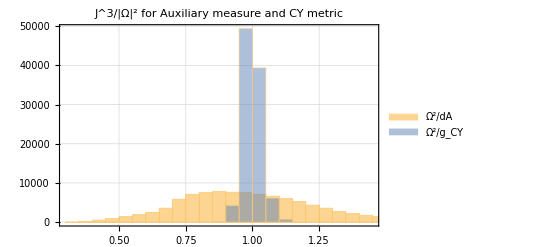

```mathematica
Histogram[{weights/Mean[weights],weightsCY/Mean[weightsCY]},PlotLabel->"J^3/|Ω|^2 for Auxiliary measure and CY metric",PlotTheme->"Detailed",ChartLegends->{ "Ω^2/dA","Ω^2/g_CY"}]
```

To actually access the CY metric, we just call CYMetric on some points

```mathematica
{metrics, session}=CYMetric[{{1,2,3,4,5}},"Model"->NNModel,"Session"->session,"Dir"->outDir];
(*NOTE: The code does not check whether the point is actually on the CY*)
```

```mathematica
{metrics, session}=CYMetric[pts,"Model"->NNModel,"Session"->session,"Dir"->outDir];
```

```mathematica
metrics[[1]]//Chop//MatrixForm
```

(0.10249-1.10595×10^-9 ⅈ | -0.0179387-0.0149531 ⅈ | 0.00820172-0.0190452 ⅈ
-0.0179387+0.0149531 ⅈ | 0.1538+1.62981×10^-9 ⅈ | 0.00396772+0.0363147 ⅈ
0.00820172+0.0190452 ⅈ | 0.00396772-0.0363147 ⅈ | 0.137763-1.28057×10^-9 ⅈ)

And the volume can be computed by integrating det(g). We compare the Kahler classes of the Fubini-Study and the CY metric, and also look at the actual value as computed from ∫J^3

```mathematica
{auxWeights,session}=GetAuxiliaryWeights["all","Dir"->outDir];
{gFSs,session}=FSMetric[pts,"Session"->session,"Dir"->outDir];
{gCYs,session}=CYMetric[pts,"Model"->NNModel,"Session"->session,"Dir"->outDir];
volFS=Round[Mean[Re[auxWeights (Det/@gFSs)]],0.1];
volCY=Round[Mean[Re[auxWeights (Det/@gCYs)]],0.1];
volInt=5;
Print["Kahler moduli:  ",{1}];
Print["Actual volume:  ",volInt];
Print["FS volume:      ",volFS];
Print["CY volume:      ",volCY];
```

Kahler moduli:  {1}

Actual volume:  5

FS volume:      5.

CY volume:      5.

For the Phi Model, we can also get the Kahler potential

```mathematica
{kahler,session}=GetKahlerPotential[pts,"Model"->NNModel,"Session"->session,"Dir"->outDir];
kahler[[;;10]]
```

{0.308325,0.261746,0.341709,0.269614,0.288271,0.288245,0.286274,0.268853,0.289151,0.299667}

### Plot losses

```mathematica
history
```

<|sigma_loss→{0.157287,0.126193,0.113318,0.0886455,0.0779465,0.0732612,0.069813,0.0688366,0.0676161,0.0670007,0.0663871,0.0660586,0.0657323,0.0654625,0.0652556,0.064955,0.0645049,0.0641964,0.0639394,0.0638384,0.063444,0.0631663,0.0626869,0.0623506,0.0619076,0.0614119,0.0607544,0.0599365,0.0585327,0.0569972,0.0552003,0.0535713,0.0516832,0.0499622,0.0479241,0.0455446,0.0432981,0.0411826,0.0395129,0.0381058,0.0371226,0.0360702,0.0354052,0.034609,0.0341559,0.0336295,0.032989,0.0326714,0.0322911,0.0321401},kaehler_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},transition_loss→{0.0087241,0.00364112,0.0050549,0.00671351,0.00585929,0.00483945,0.00392107,0.00313028,0.00261995,0.00227166,0.00203821,0.00187618,0.00174376,0.0016572,0.00158252,0.00152954,0.00149376,0.00147081,0.00144483,0.00142293,0.00141361,0.0014113,0.00142059,0.00144359,0.00145674,0.00148418,0.00154471,0.00163077,0.00176292,0.00191244,0.00207564,0.0021988,0.00228854,0.00236357,0.00248422,0.00260586,0.00270113,0.00271874,0.00272648,0.00273739,0.00273935,0.00272087,0.00271342,0.00271424,0.00270106,0.00267136,0.00266471,0.00266202,0.00263769,0.00264109},volk_loss→{0.00358414,0.0021988,0.00213367,0.00203515,0.00186826,0.00157354,0.00124093,0.00127429,0.00116479,0.0011289,0.00103567,0.00106713,0.000969433,0.000983288,0.00097906,0.000972098,0.000875527,0.00089328,0.000855265,0.000841032,0.000831277,0.000781609,0.000807624,0.000779476,0.000811754,0.00078724,0.000834581,0.000700739,0.000768884,0.000705002,0.000781237,0.000770485,0.000803283,0.00072555,0.000845738,0.000790933,0.000828358,0.000795812,0.000742816,0.000815866,0.000831879,0.000741918,0.000773593,0.00075434,0.000759544,0.000807966,0.000749253,0.000761201,0.000812198,0.000772093},sigma_val→{0.122269,0.118195,0.0992009,0.0857724,0.0832011,0.0810539,0.0768057,0.0766709,0.0742649,0.0745656,0.0749237,0.0739181,0.0738327,0.0725661,0.0751204,0.0728279,0.0737291,0.0742486,0.0711049,0.0726403,0.0713761,0.0719884,0.0713165,0.0714943,0.0708762,0.0711422,0.0688627,0.0662904,0.0655268,0.0636112,0.0601752,0.057839,0.0563796,0.0529946,0.0522716,0.0483077,0.0456805,0.0459426,0.042338,0.0391419,0.0383333,0.037841,0.0374057,0.036206,0.0358671,0.0357787,0.0358866,0.0342788,0.0352674,0.034172},kaehler_val→{5.82499×10^-15,5.8445×10^-15,5.96605×10^-15,6.30187×10^-15,6.36862×10^-15,6.35679×10^-15,6.34639×10^-15,6.30581×10^-15,6.03377×10^-15,5.99461×10^-15,6.00103×10^-15,6.10081×10^-15,6.08047×10^-15,6.02045×10^-15,6.0681×10^-15,5.95298×10^-15,6.12605×10^-15,6.06678×10^-15,6.02886×10^-15,6.08948×10^-15,6.02297×10^-15,6.0891×10^-15,6.0268×10^-15,5.9671×10^-15,6.02825×10^-15,6.02594×10^-15,6.11502×10^-15,6.09461×10^-15,6.14297×10^-15,6.07138×10^-15,6.04742×10^-15,6.16822×10^-15,6.16231×10^-15,6.21423×10^-15,6.22292×10^-15,6.19616×10^-15,6.31658×10^-15,6.21506×10^-15,6.47518×10^-15,6.2651×10^-15,6.30193×10^-15,6.35886×10^-15,6.27647×10^-15,6.25563×10^-15,6.23034×10^-15,6.39999×10^-15,6.2396×10^-15,6.25283×10^-15,6.34125×10^-15,6.31407×10^-15},transition_val→{0.00407262,0.00352976,0.00676902,0.0064467,0.00535435,0.00430118,0.00356975,0.00287577,0.00244152,0.00219198,0.00191742,0.00189351,0.00166108,0.00163891,0.00159887,0.00154481,0.00144623,0.00148015,0.00143776,0.00146202,0.00139738,0.0014879,0.00140868,0.00142136,0.00140549,0.00154396,0.00159805,0.00169707,0.00190714,0.0019721,0.00217934,0.00234013,0.00230161,0.0024225,0.00242967,0.00267486,0.0027799,0.00274285,0.00265257,0.00276355,0.00276701,0.00266116,0.00273155,0.00264228,0.00268943,0.00272081,0.00267525,0.00260582,0.00277375,0.00258642},ricci_val→{0.749761,0.59117,0.498142,0.488905,0.500591,0.483965,0.49265,0.498908,0.475239,0.477545,0.475669,0.492599,0.471202,0.499253,0.483275,0.490064,0.476198,0.486859,0.484558,0.49775,0.482364,0.486247,0.479573,0.476781,0.477849,0.476593,0.471388,0.484954,0.485254,0.453733,0.456531,0.465628,0.456696,0.454473,0.441201,0.450509,0.468784,0.466292,0.460038,0.458587,0.479648,0.465378,0.45778,0.446571,0.473906,0.450767,0.4445,0.444435,0.445203,0.436694},volk_val→{5.02257,4.99982,4.66396,4.7969,4.85053,4.88526,4.84703,4.89348,4.78631,4.83943,4.89377,4.88082,4.84592,4.8647,4.86437,4.90449,4.91585,4.91896,4.82581,4.87712,4.84647,4.91522,4.93472,4.84683,4.89599,4.86623,4.90317,4.85747,4.94855,4.92613,4.89396,4.9565,4.91944,4.97202,4.95329,4.93208,4.96241,4.98112,5.00356,4.93766,4.95518,4.95733,4.95632,4.93699,4.95701,4.97183,4.93549,4.9738,4.94853,4.96005}|>

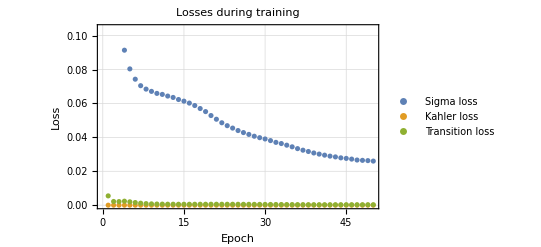

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

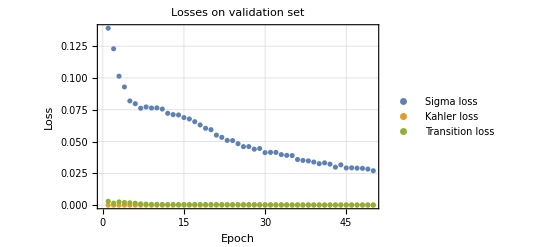

```mathematica
ListPlot[{history[["sigma_val"]],history[["kaehler_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

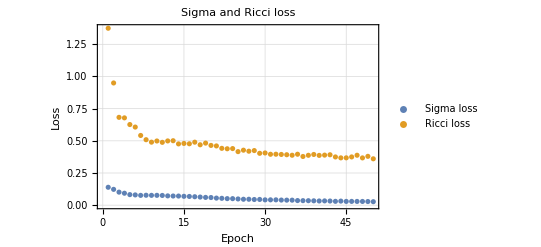

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

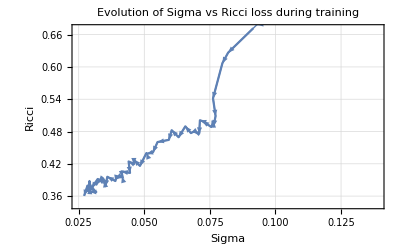

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",AxesLabel->{"Sigma","Ricci"},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Look at eigenvalues of the metric

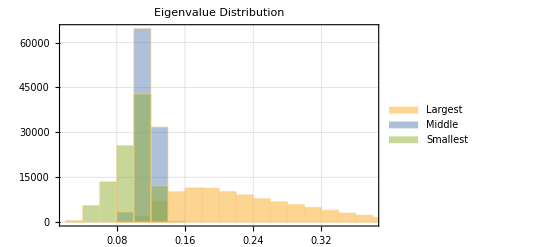

```mathematica
EigVals=Table[Eigenvalues[metrics[[i]]]//Re//Chop,{i,Length[metrics]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```